The equation that we want to solve is
θ''[r]+2/r θ'[r]+(ω^2-1)θ[r]==0
which can be cast in the following form
1/r d^2/dr^2(r θ[r])+(ω^2-1)θ[r]==0
and with the ansatz θ[r]=χ[r]/r we obtain
d^2/dr^2 χ[r]+(ω^2-1)χ[r]==0
This is the Schroedinger equation in spherical symmetry for a free particle with l=0 and negative energy. The general solution of this equation is
χ[r]=χ_+E^(√(1-ω^2)r)+χ_-E^(-√(1-ω^2)r)
The boundary condition χ[r]→0 for r→∞ translates into
χ[r]=χ_-E^(-√(1-ω^2)r)
With an extra term on the RHS the equation becomes
d^2/dr^2 χ[r]+(ω^2-1)χ[r]==r C[r]
and the complete solution is
χ_c[r]=χ_-E^(-√(1-ω^2)r)+χ_p[r]
where
d^2/dr^2 χ_p[r]+(ω^2-1)χ_p[r]==r C[r]
and then, if C[r]=C, χ_p must be linear in r
χ_p[r]==C/(ω^2-1)r
The final solution is then
θ[r]=(χ_-)/r E^(-√(1-ω^2)r)+C/(ω^2-1)
Below I prove that this is indeed the solution calculated by Mathematica

```mathematica
χm=0.1;
ω=0.8;
cc=0.;
rmax=5;
rmin=0.1;
th[r_]:=χm/r E^(-√(1-ω^2)r)+cc/(ω^2-1);
thprime[r_]:=-(E^(-r √(1-ω^2)) χm)/r^2-(E^(-r √(1-ω^2)) χm √(1-ω^2))/r;
sol=NDSolve[{θ''[r]+2/r θ'[r]+(ω^2-1)θ[r]==cc,θ[rmax]==th[rmax],θ'[rmax]==thprime[rmax]},θ[r],{r,rmin,rmax}];
θs[r_]=θ[r]/.sol;
```

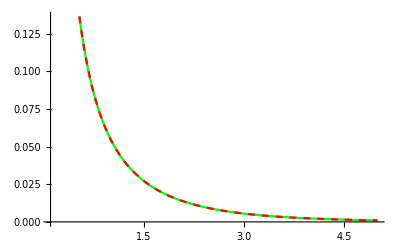

```mathematica
Plot[{θs[r],th[r]},{r,rmin,rmax},PlotStyle->{Green,{Red,Dashed}}]
```

Gravity cannot be neglected, then
θ''[r]+2/r θ'[r]+(ω^2-1+2ϕ)θ[r]==C
where in a mean field approximation
ϕ=-k_G/2 1/r
and then
θ''[r]+2/r θ'[r]+(ω^2-1-k_G/r)θ[r]==C
(*****************************************************************************
Rewriting it in terms of θ[r]=χ[r]/r,
d^2/dr^2 χ[r]+(ω^2-1-k_G/r)χ[r]==C r
for r→0 the solution of the simplified equation
d^2/dr^2 χ[r]-k_G/r χ[r]=0
is a Bessel function
χ=χ_1 √(k_G r)I_1(2 √(k_G r))+χ_2 √(k_G r)K_1(2 √(k_G r))
And for large radii, assuming that C vanishes at infinity, we recover the exponential solutions of the first case (solutions of d^2/dr^2 χ[r]+(ω^2-1)χ[r]==0)
******************************************************************************)
The stability of the clump can be described by this equation, which sounds like a stationary Schroedinger equation with (1-ω^2) as energy
θ''[r]+2/r θ'[r]-k_G/r θ[r]-C==(1-ω^2)θ[r]
assuming an exponential ansatz (because C vanishes somewhere at infinity)
θ[r]=θ_0 E^(-r/R)
the Hamiltonian is easily identified as (the Hertzberg's one plus the C term coming from -g_aγ E·B∫d^3 x θ)
H_eff=N/(2 R^2)-(5 N^2)/(16 R)-N^2/(128π R^3)-2C R^3
Extremizing for R we have
0=-R+(5N)/16 R^2+(3N)/(128π)-(6C R^6)/N
Which is solved below to give the stability radii

```mathematica
n=9;
c=10;
Print["c≠0 case, note the presence of another (un)stable solution depending on the sign of c"]
NSolve[-R+(5n)/16 R^2+(3n)/(128π)-(6c R^6)/n==0,R]
Print["c=0 case"]
8./(5n)-(√(512π-15 n^2))/(10 √(2π)n)
8./(5n)+(√(512π-15 n^2))/(10 √(2π)n)
```

c≠0 case, note the presence of another (un)stable solution depending on the sign of c

{{R→-0.881907},{R→-0.0839185-0.820989 ⅈ},{R→-0.0839185+0.820989 ⅈ},{R→0.0898406},{R→0.270881},{R→0.689023}}

c=0 case

0.0898477

0.265708

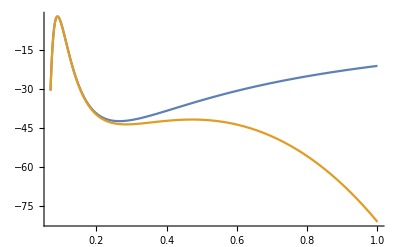

```mathematica
n=9;
c=30;
H[n_,c_,r_]:=n/(2 r^2)-5/16 n^2/r-n^2/(128π r^3)-2c r^3;
Plot[{H[n,0,r],H[n,c,r]},{r,0.07,1},PlotRange->All]
```